```mathematica
(*For a constant liquidlevel inside the tube, the number of particles per time flowing through the liquid part of the tube to the boundary has to equal the number of particles per time evaporating from the boundary. So I combined the hagen poiseuille equation for the liquid part  with the throughput equation for the gas part *)

r=0.00002 ; (*tube radius*); d=2*r;  (*tube diameter*)
l=0.0001; (*tube length*)
k=1.38064852*10^(-23); (*Boltzmann Constant*)
T=273.15+25; (*room temperature*)
rho=997; (*water density*)
NA=6.02214086*10^23 ; (*Avogadro Constant*)
my=0.00089; (*water dynamic viscosity*)
m=0.018015/NA ;(*mass of a single water molecule*)
pv=3168.5747474290; (*vapour pressure water at room temperature*)
va=Sqrt[(8*k*T)/(Pi*m)] ;(*average velocity of water molecule in gas*)
K=(8*my*m*pv*va)/(d*d*rho*k*T); 

p0[h_]:=pv+K*(14l+4l/d*h-14h-4/d*h*h)/(14+18/d*h+3/d/d*h*h)

Solve[p==pv+K*(14l+4l/d*h-14h-4/d*h*h)/(14+18/d*h+3/d/d*h*h)&& 0<h<l,h,Reals] (*Find the inverse function h(p)*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{h→ConditionalExpression[-(1.47712×10^-17 (-3.84997×10^22+1.21525×10^19 p))/(-4.73502×10^9+1.4959×10^6 p)+1.39553×10^-32 √((7.98497×10^74-5.04432×10^71 p+7.96658×10^67 p^2)/((-4.73502×10^9+1.4959×10^6 p)^2)),3168.57<p<3174.66]}}

```mathematica
h[p_]:=(-(1.4771237849202934*^-17 (-3.849967250619187*^22+1.2152544142377777*^19 p))/(-4.735020319*^9+1.495901*^6 p)+1.3955259361199774*^-32 √((7.984969152366471*^74-5.044315894239359*^71 p+7.966580713426784*^67 p^2)/((-4.735020319*^9+1.495901*^6 p)^2)))

z[p_]:=l-h[p] (*z-coordinate of the liquidlevel inside the tube*)
```

```mathematica
z[5000]
```

0.000136583

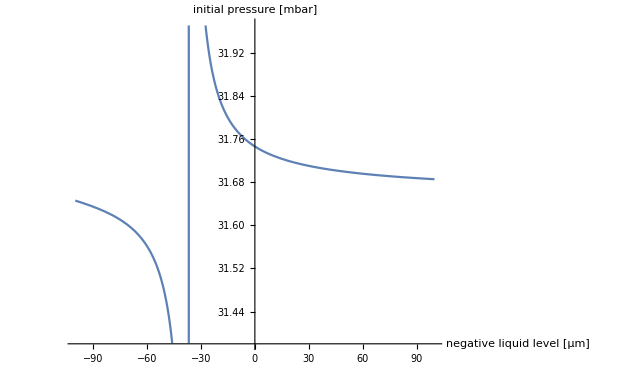

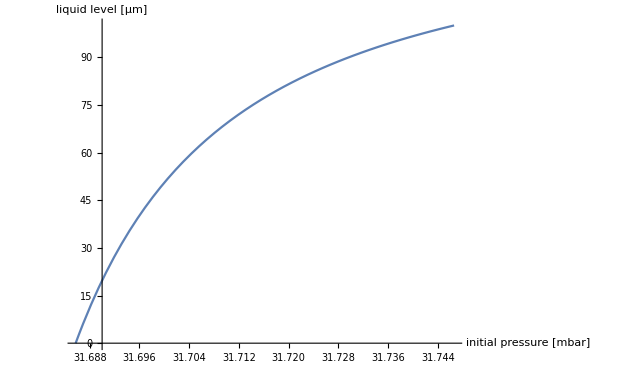

```mathematica
Plot[{p0[h/10^6]/100},{h,-l*10^6,l*10^6},AxesLabel->{"negative liquid level [μm]","initial pressure [mbar]"}]
Plot[{(z[100p]*10^6)},{p,pv/100,3174.658640498029/100},AxesLabel->{"initial pressure [mbar]","liquid level [μm]"}]

(*line1=Line[{{8.81372,0},{8.81372,l*10^6}}];
Plot[{(z[100000p]*10^6),l*10^6},{p,0,11},
PlotStyle->{Automatic,Directive[lineStyle],Directive[lineStyle]},Epilog->{Directive[lineStyle],line1},
AxesLabel->{"initial pressure [bar]","liquid level [μm]"}]*)
```